# Basic function shapes

## Power function

f(x)=a x^b

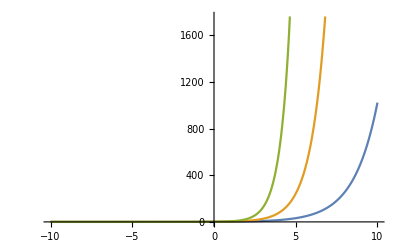

```mathematica
Plot[{f3[2,n],f3[3,n],f3[5,n]},{n,-10,10}]
```

## Exponential function

f(x)=a b^x

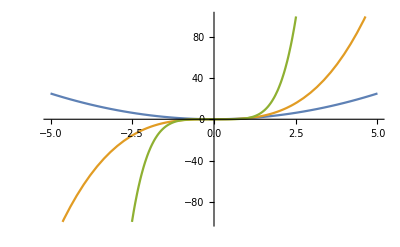

```mathematica
f3[x_,n_]:=x^n
Plot[{f3[x,2],f3[x,3],f3[x,5]},{x,-5,5}]
```

## Logarithmic function

Informally, a logarithm is an “inverse” of an exponentiation.
An exponentiated variable is the value the variable assumes when exponentiated (that is, multiplied by itself) a certain number of times.
The logarithm of a variable is the exponent a variable must exhibit (that is, how many times it must be multiplied by itself) to assume a certain value.

f(x)=log_b x

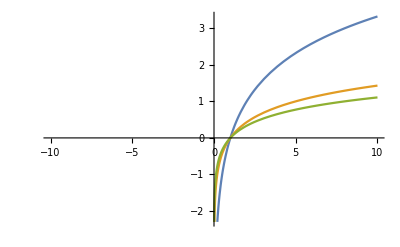

```mathematica
f4[x_,b_]:=Log[b,x]
Plot[{f4[x,2],f4[x,5],f4[x,8]},{x,-10,10}]
```

f(x)=log_b x

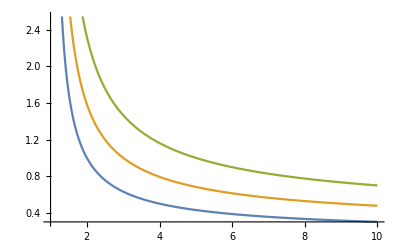

```mathematica
Plot[{f4[2,b],f4[3,b],f4[5,b]},{b,1,10}]
```

## Polynomial function

The polynomial function possesses a degree value indicated by the highest exponent in all of its terms.
It exhibits an added inflection point or, informally, is a  “one step” more complex curve with each higher degree.

## Degree 1 polynomial

f(x)=2 x^1+3 x^0

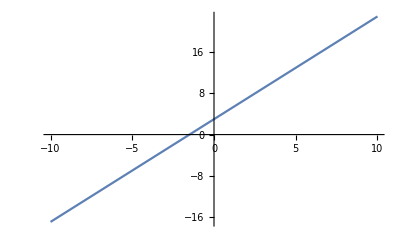

```mathematica
fp1[x_, a1_,a0_]:=a1*x^1+a0*x^0
Plot[fp1[x,2,3],{x,-10,10}]
```

```mathematica
Manipulate[Plot[fp1[x,a1,a0],{x,-10,10},PlotRange->{{-10,10},{-10,10}}],{{a1,2},-20,20,0.1},{{a0,0},-20,20,0.1}]
```

## Degree 2 polynomial

Function declaration:

```mathematica
fp2[x_, a2_,a1_,a0_]:=a2*x^2+a1*x^1+a0*x^0
```

```mathematica
Manipulate[Plot[fp2[x,a2,a1,a0],{x,-10,10},PlotRange->Automatic],{{a2,2},-3,3,0.1},{{a1,2},-30,30,0.1},{{a0,0},-30,30,0.1}]
```

Curve of interest: 1.9 x^2+26.2 x^1-28.4 x^0.

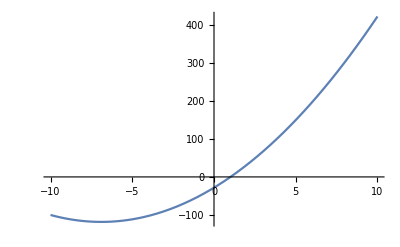

```mathematica
Plot[fp2[x,1.9,26.2,-28.4],{x,-10,10}]
```

## Degree 3 polynomial

Function declaration:

```mathematica
fp3[x_, a3_,a2_,a1_,a0_]:=a3*x^3+a2*x^2+a1*x^1+a0*x^0
```

```mathematica
Manipulate[Plot[fp3[x,a3,a2,a1,a0],{x,-10,10},PlotRange->Automatic],{{a3,1},-2,2,0.1},{{a2,2},-8,8,0.1},{{a1,2},-150,150,0.1},{{a0,0},-300,300,0.1}]
```

Curve of interest: 0.1 x^3-2 x^2+10.3 x^1-8.1 x^0.

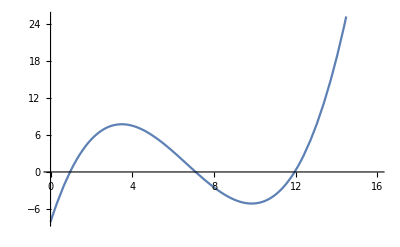

```mathematica
Plot[fp3[x,0.1,-2,10.3,-8.1],{x,0,16}]
```

## Degree 4 polynomial

Function declaration:

```mathematica
fp4[x_, a4_,a3_,a2_,a1_,a0_]:=a4*x^4+a3*x^3+a2*x^2+a1*x^1+a0*x^0
```

```mathematica
Manipulate[Plot[fp4[x,a4,a3,a2,a1,a0],{x,-10,10},PlotRange->Automatic],{{a4,1},-1.002,1.002,0.02},{{a3,1},-2,2,0.1},{{a2,2},-12,12,0.1},{{a1,2},-150,150,0.1},{{a0,0},-300,300,0.1}]
```

Curve of interest: -0.102 x^4+0.6 x^3+12 x^2-96 x^1+239.7 x^0.

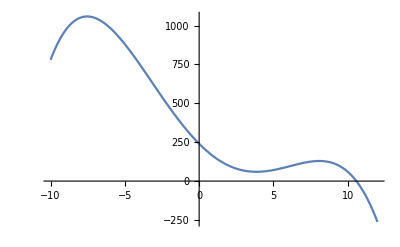

```mathematica
Plot[fp4[x,-0.102,0.6,12,-96,239.7],{x,-10,12}]
```

Curve of interest: -0.222 x^4+0 x^3+12 x^2+5.6 x^1+0 x^0.

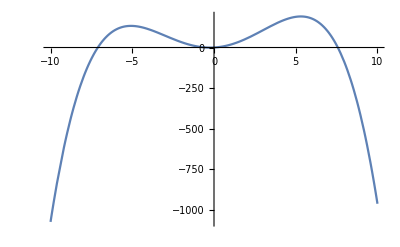

```mathematica
Plot[fp4[x,-0.222,0,12,5.6,0],{x,-10,10}]
```

## Degree 5 polynomial

With each higher degree, the input into the complexity of the shape becomes greater of the highest parameters in the polynomial, that is, the terms with highest coefficients.

The lower degree terms necessitate exhibiting higher magnitude coefficients to impart the same effect on the shape of the curve, than the higher degree terms can with just lower magnitude coefficients.

Function declaration:

```mathematica
fp5[x_, a5_,a4_,a3_,a2_,a1_,a0_]:=a5*x^5+a4*x^4+a3*x^3+a2*x^2+a1*x^1+a0*x^0
```

```mathematica
Manipulate[Plot[fp5[x,a5,a4,a3,a2,a1,a0],{x,-10,10},PlotRange->Automatic],{{a5,0},-1.00000000001,1.00000000001,0.00000001},{{a4,0},-1.0000001,1.0000001,0.000001},{{a3,1},-2,2,0.1},{{a2,2},-12,12,0.1},{{a1,2},-150,150,0.1},{{a0,0},-300,300,0.1}]
```

Curve of interest: -0.015873 x^5 -0.0582011 x^4+1 x^3+2 x^2+2 x^1+0 x^0.

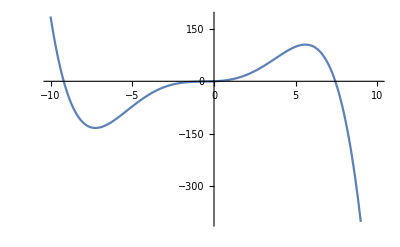

```mathematica
Plot[fp5[x,-0.015873,-0.0582011,1,2,2,0],{x,-10,10}]
```

Curve of interest: -0.026455 x^5 +0.0052909 x^4+1.6 x^3+5 x^2-16.7 x^1-7.9 x^0.

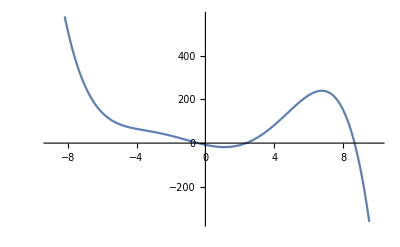

```mathematica
Plot[fp5[x,-0.026455,0.0052909,1.6,5,-16.7,-7.9],{x,1-10,10}]
```

## Degree 6 polynomial

Function declaration:

```mathematica
fp6[x_, a6_,a5_,a4_,a3_,a2_,a1_,a0_]:=a6*x^6+a5*x^5+a4*x^4+a3*x^3+a2*x^2+a1*x^1+a0*x^0
```

```mathematica
Manipulate[Plot[fp6[x,a6,a5,a4,a3,a2,a1,a0],{x,-2,2},PlotRange->Automatic],{{a6,0}, -1.00000001,1.00000001,0.00000000000001},{{a5,0},-1.00000001,1.00000001,0.00001},{{a4,0},-1.0001,1.0001,0.001},{{a3,1},-2,2,0.1},{{a2,2},-12,12,0.1},{{a1,2},-150,150,0.1},{{a0,0},-300,300,0.1}]
```

Curve of interest: -0.269841 x^6-0.51323 x^5 +0.8939 x^4+2 x^3-0.2 x^2-0.8 x^1+1.6 x^0.

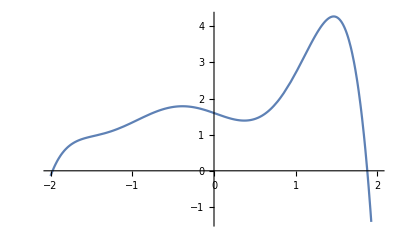

```mathematica
Plot[fp6[x,-0.269841,-0.51323,0.8939,2,-0.2,-0.8,1.6],{x,-2,2}]
```

This looks like a montainous landscape.

Curve of interest: 0.111111 x^6-1 x^5 +0.9999 x^4+2 x^3-1.2 x^2-2.4 x^1-1.6 x^0.

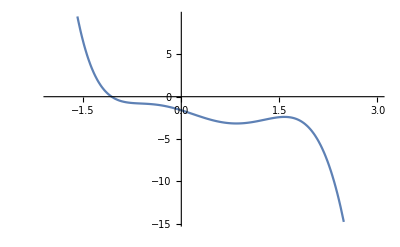

```mathematica
Plot[fp6[x,0.111111,-1,0.9999,2,-1.2,-2.4,-1.6],{x,-2,3}]
```

## Sinusoidal function

Function declaration:

```mathematica
fs[x_,a_,b_,c_,d_]:=a+b*Sin[c*x+d]
```

f(x)=a +b sin(cx+d)

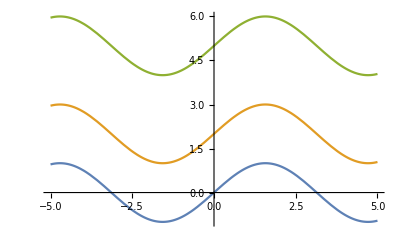

```mathematica
Plot[{fs[x,0,1,1,0],fs[x,2,1,1,0],fs[x,5,1,1,0]},{x,-5,5}]
```

f(x)=a +b sin(cx+d)

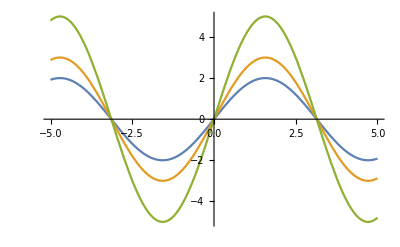

```mathematica
Plot[{fs[x,0,2,1,0],fs[x,0,3,1,0],fs[x,0,5,1,0]},{x,-5,5}]
```

f(x)=a +b sin(cx+d)

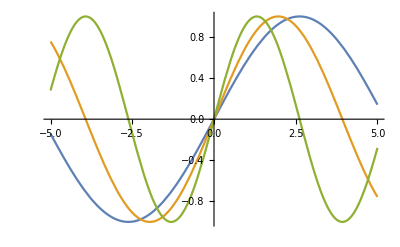

```mathematica
Plot[{fs[x,0,1,.6,0],fs[x,0,1,.8,0],fs[x,0,1,1.2,0]},{x,-5,5}]
```

f(x)=a +b sin(cx+d)

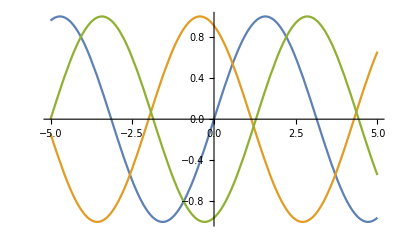

```mathematica
Plot[{fs[x,0,1,1,0],fs[x,0,1,1,2],fs[x,0,1,1,5]},{x,-5,5}]
```

f(x)=a +b sin(c x+d) (parameter values open to manipulation):

```mathematica
Manipulate[Plot[fs[x,a, b, c, d],{x,-5,5},PlotRange->{{-5,5},{-1.2,1.2}}],{{a,0},-2,2,.1},{{b,1},-5,5,.1},{{c,1},-10,10,.1},{{d,0},-10,10,.1}]
```

## Curve fitting

Fitting means finding approximations of curves by other curves.

For example, a curve might be complex enough that finding its exact polynomial might be too difficult. Instead, a similar enough curve can be found that gives sufficient precision solutions to a problem.

A polynomial curve might have enough inflection points, that is, a high enough degree, to exhibit a similar shape to another curve. The coefficients of each term will also need to be adjusted to find the best fit.

One technique for finding such adjustment for coefficients is simply superimposing the more complex and less complex curves and taking the difference at each point of consideration, that is, using a collection of points established to be used as a guide.

With a polynomial curve, these points might be the inflection points of the terms of the polynomial. The inflection points are equal in number to the number of terms.

If the difference in each point is taken as the term of a function of squares that represents the summing of the differences, for example:

f(a,b,c,d,e)=0.1 a^2+0.3 b^2-0.4 c^2+0.21 d^2-0.05 e^2,

for a 5-term polynomial (where 0.1, 0.3, -0.4, 0.21, -0.05 are the observed differences), then the sum that yields the lowest value overall indicates the best fit curve.

This lowest value can be found by setting the derivative function of each variable to zero. For n variables, a system of n equations result which, when solved, give the best value for each variable.

## 8-point series fit: degree 7 polynomial.

The black dots represent the observed complex curve and the blue line is the solution (calculated elsewhere).

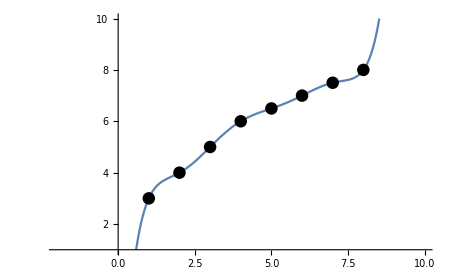

```mathematica
t={1,2,3,4,5,6,7,8};
v={3,4,5,6,6.5,7,7.5,8};
ts=TimeSeries[v,{t}];
fp7[x_, a7_,a6_,a5_,a4_,a3_,a2_,a1_,a0_]:=a7*x^7+a6*x^6+a5*x^5+a4*x^4+a3*x^3+a2*x^2+a1*x^1+a0*x^0
Show[Plot[fp7[x,0.00099206,-0.03194444,0.41944444,-2.88194445,11.04861112,-23.33611114,25.78095241,-8.00000001],{x,-2,10},PlotRange->{{-2,10},{1,10}},ImageSize->450],
ListPlot[ts, PlotStyle->{PointSize[.02],Black}]]
```